```mathematica
Remove["Global`*"]
```

```mathematica
Subscript[T, air]=261.15;
Alac= 18500;
Subscript[T, fond]= 281.15;
Subscript[T, init] = 281.15;
Subscript[T, cible] = 277.13;
A1= 1.946*^4;
A2 = 2.188*^4;
C1 = 1.549*^8;
C2 = 5.420*^8;
```

```mathematica
solq1 = DSolve[{Q'[τ] == -Alac Subscript[T, air]-α A1 Subscript[T, fond] + (Subscript[T, init]-Q[τ]/C1)(Alac+α A1), Q[0] == 0}, Q[τ],τ];
Q1[τ_, a_] = Q[τ] /. solq1 /. α -> a;
solq2 = DSolve[{Q'[τ] == -Alac Subscript[T, air]-α A2 Subscript[T, fond] + (Subscript[T, init]-Q[τ]/C2)(Alac+α A2), Q[0] == 0}, Q[τ],τ];
Q2[τ_, a_] = Q[τ] /. solq2 /. α -> a;
```

```mathematica
T1[t_, a_] = Simplify[Subscript[T, init]-Q1[t,a]/C1]
T2[t_, a_] = Simplify[Subscript[T, init]-Q2[t,a]/C2]
```

{281.15+(-19.0134+19.0134 ⅇ^((-0.000119432-0.000125629 a) t))/(0.950668+1. a)}

{281.15+(-16.9104+16.9104 ⅇ^((-0.0000341328-0.000040369 a) t))/(0.845521+1. a)}

```mathematica
target = Subscript[T, cible];
findEnd[f_, a_] = t /. Solve[f[t, a] ==  target,t][[1]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tFin5 = {findEnd[T1, 0.5],findEnd[T2, 0.5]}
tFin2 = {findEnd[T1, 2],findEnd[T2, 2]}
tFin4 = {findEnd[T1, 3],findEnd[T2, 3]}
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{2009.99,7096.43}

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{2637.77,9823.13}

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{3633.89,15816.7}

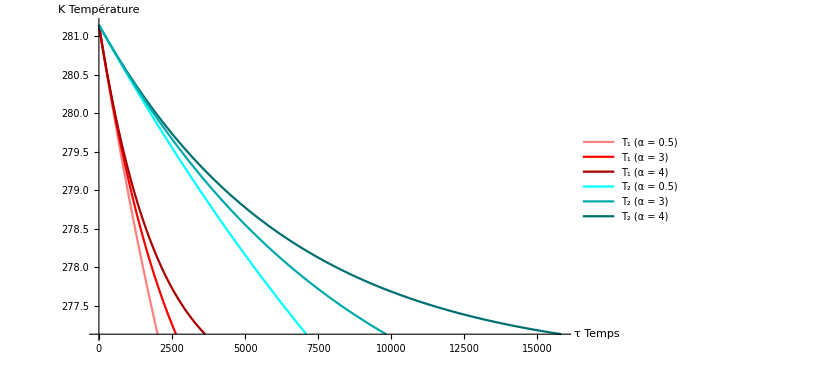

```mathematica
g15 = Plot[T1[t,0.5], {t,0,tFin5[[1]]}, PlotStyle -> Pink];
g12 = Plot[T1[t,2], {t,0,tFin2[[1]]}, PlotStyle -> Red];
g14 = Plot[T1[t,3], {t,0,tFin4[[1]]}, PlotStyle -> Darker[Red]];
g25 = Plot[T2[t,0.5], {t,0,tFin5[[2]]}, PlotStyle -> Cyan];
g22 = Plot[T2[t,2], {t,0,tFin2[[2]]}, PlotStyle -> Darker[Cyan]];
g24 = Plot[T2[t,3], {t,0,tFin4[[2]]}, PlotStyle -> Darker[Darker[Cyan]], AxesLabel -> {τ Temps,K Température}, PlotLegends -> Placed[LineLegend[{Pink,Red,Darker[Red],Cyan,Darker[Cyan],Darker[Darker[Cyan]]}, {"T_1 (α = 0.5)","T_1 (α = 3)","T_1 (α = 4)", "T_2 (α = 0.5)","T_2 (α = 3)","T_2 (α = 4)"}],{0.8,0.8}]];
Show[g24,g15,g12,g14,g25,g22]
```